```mathematica
maxGDUcoefficient[0, 0, 0, 0, 0, 0] // Timing
```

{18.,2.39035×10^-6}

```mathematica
HammingWindow[x] // FunctionExpand
```

```mathematica
qqq[x_] :=Piecewise[{{25/46+21/46 Cos[2 π x], -1/2≤x≤1/2}, {0, True}}]
```

```mathematica
Function[t,Piecewise[{{25/46+21/46 Cos[2 π t],-1/2≤t≤1/2}},0]] // FunctionExpand
```

Function[t,Piecewise[{{25/46+21/46 Cos[2 π t], -1/2≤t≤1/2}, {0, True}}]]

Piecewise[{{25/46+21/46 Cos[2 π q], -1/2≤q≤1/2}, {0, True}}]

```mathematica
(π/ArcSin[1/Sqrt[15]] - 2)/4
```

```mathematica
Tmax // N
```

5.×10^-6

```mathematica
Tmax = 10^-6
```

1/1000000

```mathematica
MatrixExp[ⅈ*a*{{0, 0}, {1, 0}}] // MatrixForm
```

(1 | 0
ⅈ a | 1)

```mathematica
basisGERotated = {"|g↓⇓>", "|g↓⇑>", "|g↑⇓> + |e↓⇑>", "|g↑⇑>", "|e↓⇓>", "|g↑⇓> - |e↓⇑>", "|e↑⇓>", "|e↑⇑>"};

setVariables[]
ΔE = 0;
Bac = 0;
Eac = 0;

Clear[B0];
B0sol = NSolve[H[[3]][[3]] == H[[6]][[6]], B0][[1]]
B0 = (B0 /. B0sol);

Λ = IdentityMatrix[8];
Λ[[3]][[3]] = 1/Sqrt[2];
Λ[[3]][[6]] = 1/Sqrt[2];
Λ[[6]][[3]] = 1/Sqrt[2];
Λ[[6]][[6]] = -1/Sqrt[2];
Λ // MatrixForm;

clearVariables[]
Htrans = transform[H, Λ];
setVariables[]
ΔE = 0;
B0 = (B0 /. B0sol);

printWithBasis[Htrans // FullSimplify, basisGERotated]


Bac = 0;
Eac = 0;

energiesInOrder[0, Htrans]

statesInOrder[0, Htrans] // MatrixForm
clearVariables[]
```

{B0→0.201123}

( | |g↓⇓> | |g↓⇑> | |g↑⇓> + |e↓⇑> | |g↑⇑> | |e↓⇓> | |g↑⇓> - |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | -5.60516×10^9 | -8.615×10^6 Bac | 9.88889×10^9 Bac | 0 | 1.74377×10^7-1.81349×10^6 Eac | 9.88889×10^9 Bac | 0 | 0
|g↓⇑> | -8.615×10^6 Bac | -5.63788×10^9 | 1.23303×10^7-1.28233×10^6 Eac | 1.3985×10^10 Bac | 0 | 2.90354×10^7+1.28233×10^6 Eac | 2.925×10^7 | 0
|g↑⇓> + |e↓⇑> | 9.88889×10^9 Bac | 1.23303×10^7-1.28233×10^6 Eac | 1.4625×10^7 | -6.09172×10^6 Bac | -6.09172×10^6 Bac | 0. | 8.35255×10^6-1.28233×10^6 Eac | 9.88889×10^9 Bac
|g↑⇑> | 0 | 1.3985×10^10 Bac | -6.09172×10^6 Bac | 1.11597×10^7 | 0 | -6.09172×10^6 Bac | 0 | 1.18123×10^7-1.81349×10^6 Eac
|e↓⇓> | 1.74377×10^7-1.81349×10^6 Eac | 0 | -6.09172×10^6 Bac | 0 | 1.80903×10^7 | 6.09172×10^6 Bac | 1.3985×10^10 Bac | 0
|g↑⇓> - |e↓⇑> | 9.88889×10^9 Bac | 2.90354×10^7+1.28233×10^6 Eac | 0. | -6.09172×10^6 Bac | 6.09172×10^6 Bac | -4.3875×10^7 | -3.30132×10^7-1.28233×10^6 Eac | -9.88889×10^9 Bac
|e↑⇓> | 0 | 2.925×10^7 | 8.35255×10^6-1.28233×10^6 Eac | 0 | 1.3985×10^10 Bac | -3.30132×10^7-1.28233×10^6 Eac | 5.60863×10^9 | -8.615×10^6 Bac
|e↑⇑> | 0 | 0 | 9.88889×10^9 Bac | 1.18123×10^7-1.81349×10^6 Eac | 0 | -9.88889×10^9 Bac | -8.615×10^6 Bac | 5.63441×10^9)

{-5.60521×10^9,-5.63813×10^9,1.46395×10^7,1.11348×10^7,1.81444×10^7,-4.39155×10^7,5.60891×10^9,5.63443×10^9}

(0.999995 | -6.10907×10^-19 | -1.93252×10^-17 | 0. | -0.00310096 | 0. | -3.2951×10^-19 | 0.
0. | 0.999981 | -0.00217739 | 0. | -1.11022×10^-16 | -0.00520555 | -0.00261436 | 0.
0. | -0.00218354 | -0.999995 | 0. | 6.23199×10^-15 | -0.00192593 | 0.00149317 | 0.
0. | 0. | 0. | -0.999998 | 0. | 0. | 0. | 0.0021006
-0.00310096 | -2.86716×10^-16 | -6.23198×10^-15 | 0. | -0.999995 | 0. | -9.49176×10^-17 | 0.
0. | 0.00521649 | -0.00192858 | 0. | 1.25767×10^-17 | 0.999968 | 0.00581608 | 0.
0. | 0.00258729 | 0.00149872 | 0. | 0. | -0.00582675 | 0.999979 | 0.
0. | 0. | 0. | 0.0021006 | 0. | 0. | 0. | 0.999998)

(50.04 | -0.0399681 | 0.
{0.019976,0.019976,0.999601} | {-0.706825,-0.706825,0.0282504} | {0.707107,-0.707107,0.})

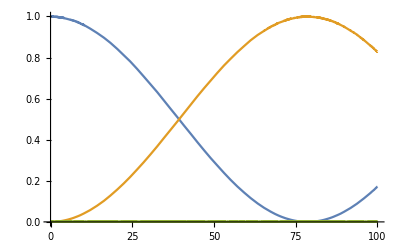

```mathematica
Ω1 = 1;
Ω2 = 1;
MM = {{0, 0, Ω1}, {0, 0, Ω2}, {Ω1, Ω2, 50.0}};
ψO = {1, 0, 0};

Eigensystem[MM] // MatrixForm

ψ[t_] := MatrixExp[-ⅈ*MM*t].ψO
Plot[{Abs[(ψ[t][[1]])^2],Abs[(ψ[t][[2]])^2], Abs[(ψ[t][[3]])^2]}, {t, 0, 100}]
```

(Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,4] | Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,3] | Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,1] | Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,2]
{(-20000000+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,4])/100000,(300000000000000000+199980000000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,4]-30000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,4]^2+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,4]^3)/1000000000000000,(-10000000000-20000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,4]+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,4]^2)/10000000000,1} | {(-20000000+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,3])/100000,(300000000000000000+199980000000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,3]-30000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,3]^2+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,3]^3)/1000000000000000,(-10000000000-20000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,3]+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,3]^2)/10000000000,1} | {(-20000000+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,1])/100000,(300000000000000000+199980000000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,1]-30000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,1]^2+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,1]^3)/1000000000000000,(-10000000000-20000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,1]+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,1]^2)/10000000000,1} | {(-20000000+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,2])/100000,(300000000000000000+199980000000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,2]-30000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,2]^2+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,2]^3)/1000000000000000,(-10000000000-20000000 Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,2]+Root[100000000000000000000+500000000000000000 #1+199970000000000 #1^2-30000000 #1^3+#1^4&,2]^2)/10000000000,1})

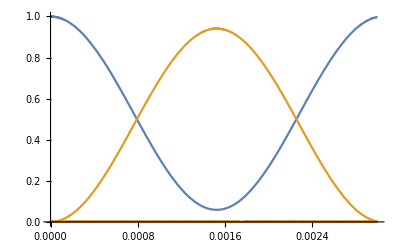

```mathematica
Ω1 = 10^5;
Ω2 = 10^5;
ϵ = 10^7;
Δ2 = 10^7;
MM = {{0, 0, Ω1, Ω1}, {0, 0, Ω2, -0*Ω2}, {Ω1, Ω2, ϵ, 0}, {Ω1, -0*Ω2, 0, ϵ + Δ2}};

Eigensystem[MM] // MatrixForm

ψO = {1, 0, 0, 0};
ψ[t_] := MatrixExp[-ⅈ*MM*t].ψO
Plot[{Abs[(ψ[t][[1]])^2],Abs[(ψ[t][[2]])^2], Abs[(ψ[t][[3]])^2], Abs[(ψ[t][[4]])^2]}, {t, 0, 3*10^-3}]
```

{B0→0.201123}

{ωMid,ωGap,1.13665×10^8}

1.83783×10^8

{{-3.52183×10^10,0,8.05713×10^6 Cos[3.51264×10^10 t],8.05713×10^6 Cos[3.51264×10^10 t]},{0,-3.54238×10^10,7.74737×10^7-8.05713×10^6 Cos[3.53319×10^10 t],1.82435×10^8+8.05713×10^6 Cos[3.53319×10^10 t]},{8.05713×10^6 Cos[3.51264×10^10 t],7.74737×10^7-8.05713×10^6 Cos[3.53319×10^10 t],9.18916×10^7,0.},{8.05713×10^6 Cos[3.51264×10^10 t],1.82435×10^8+8.05713×10^6 Cos[3.53319×10^10 t],0.,-2.75675×10^8}}

( | |g↓⇓> | |g↓⇑> | |g↑⇓> + |e↓⇑> | |g↑⇑> | |e↓⇓> | |g↑⇓> - |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | -3.52183×10^10 | 0 | 8.05713×10^6 Cos[3.51264×10^10 t] | 0 | 0 | 8.05713×10^6 Cos[3.51264×10^10 t] | 0 | 0
|g↓⇑> | 0 | -3.54238×10^10 | 7.74737×10^7-8.05713×10^6 Cos[3.53319×10^10 t] | 0 | 0 | 1.82435×10^8+8.05713×10^6 Cos[3.53319×10^10 t] | 0 | 0
|g↑⇓> + |e↓⇑> | 8.05713×10^6 Cos[3.51264×10^10 t] | 7.74737×10^7-8.05713×10^6 Cos[3.53319×10^10 t] | 9.18916×10^7 | 0 | 0 | 0. | 0 | 0
|g↑⇑> | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|e↓⇓> | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|g↑⇓> - |e↓⇑> | 8.05713×10^6 Cos[3.51264×10^10 t] | 1.82435×10^8+8.05713×10^6 Cos[3.53319×10^10 t] | 0. | 0 | 0 | -2.75675×10^8 | 0 | 0
|e↑⇓> | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
|e↑⇑> | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

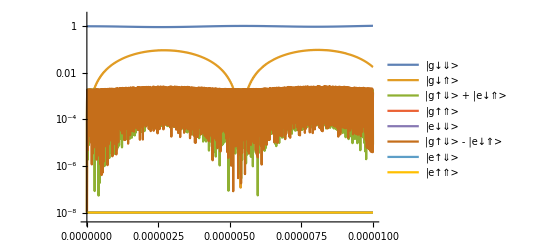

```mathematica
Htrans = transform[H, Λ];

setVariables[]
Clear[ψ]

ΔE = 0;
Bac = 0;
Eac = 0;

Clear[B0];
B0sol = NSolve[H[[3]][[3]] == H[[6]][[6]], B0][[1]]
B0 = (B0 /. B0sol);

Clear[Bac]
Clear[Eac]

M = 2*π*H;
Mtrans = 2*π*Htrans;

{ωMid, ωGap, Mtrans[[5]][[5]]}

Do[
Do[
If[!((j == 1 || j == 2 || j == 3 || j == 6) && (i == 1 || i == 2 || i == 3 || i == 6)), Mtrans[[i]][[j]] = 0]
,{j, 1, 8}]
,{i, 1, 8}]

Mtrans[[1]][[2]] = 0;
Mtrans[[2]][[1]] = 0;

ωGap = Mtrans[[3]][[3]] - Mtrans[[6]][[6]];
ω1 = (Mtrans[[6]][[6]] - ωGap) - Mtrans[[1]][[1]];
ω2 = (Mtrans[[6]][[6]] - ωGap) - Mtrans[[2]][[2]];

ωMid = (Mtrans[[6]][[6]] + Mtrans[[3]][[3]])/2;
ω1 = ωMid - Mtrans[[1]][[1]];
ω2 = ωMid - Mtrans[[2]][[2]];

(Mtrans[[3]][[3]] - Mtrans[[1]][[1]]) - ω1

Mtrans4x4 = Mtrans[[{1, 2, 3, 6}, {1, 2, 3, 6}]] // FullSimplify;

(*printWithBasis[Mtrans // FullSimplify, basisGERotated]*)

Eac = 1*Cos[ω2*t];
Bac = 0;
 Bac = 1*((8.057132424585237*^6)/(6.213371789014474*^10))Cos[ω1*t]; 

Mtrans[[{1, 2, 3, 6}, {1, 2, 3, 6}]] // FullSimplify

Tmax = 10*10^-6;

(*printWithBasis[Mtrans // FullSimplify, basisGERotated]*)

U0 = IdentityMatrix[8]*E^(ⅈ*Mtrans[[1]][[1]]*t);
U = DiagonalMatrix[{1, E^(ⅈ(ω1 - ω2)*t), E^(ⅈ*ω1*t), 1, 1, E^(ⅈ*ω1*t), 1, 1}];
(*Mtrans = transform[Mtrans, U0] // FullSimplify;*)
(*Mtrans = transform[Mtrans, U] // FullSimplify // Chop;*)
Mtrans = Mtrans // FullSimplify;
printWithBasis[Mtrans, basisGERotated]

ψ0 = {1, 0, 0, 0, 0, 0, 0, 0};

funcs=Array[ψ[#1][t]&,{Length[ψ0]}];

equations=Flatten@Join[Thread[Mtrans.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];

state= NDSolveValue[equations,funcs,{t,-Tmax/100,101*Tmax/100}];

LogPlot[Evaluate@Table[Max[Abs[state[[i]]]^2, 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All, PlotLegends->basisGERotated]

clearVariables[]
```

```mathematica
clearVariables[];

Htrans = transform[H, Λ];

setVariables[]
Clear[ψ]

ΔE = 0;
Bac = 0;
Eac = 0;

Clear[B0];
B0sol = NSolve[H[[3]][[3]] == H[[6]][[6]], B0][[1]]
B0 = (B0 /. B0sol);

Clear[Bac]
Clear[Eac]

M = 2*π*H;
Mtrans = 2*π*Htrans // FullSimplify;

ω1 = 168*n;
ω2 = 169*n;

(*Eac = 20*Cos[(ω2 + δ2)*t] + (7.74736821604787*^7 - 1.8243496972178563*^8)/(2*8.057132424585237*^6 );
 Bac = 20*((8.057132424585237*^6)/(6.213371789014474*^10))Cos[(ω1 + δ1)*t];
Mtrans // FullSimplify // MatrixForm*)

Clear[peakP];
peakP[δ1_?NumericQ, δ2_?NumericQ] := (

a = 1;

(* set Eac and Bac *)
Eac = 12*Cos[(ω2 + δ2)*t] + (7.74736821604787*^7 - 1.8243496972178563*^8)/(2*8.057132424585237*^6 );
 Bac = a*12*((8.057132424585237*^6)/(6.213371789014474*^10))Cos[(ω1 + δ1)*t];

(* set simulation length *)
Tmax = 300/n;


Clear[ψ];
ψ0 = {1, 0, 0, 0, 0, 0, 0, 0};
funcs=Array[ψ[#1][t]&,{Length[ψ0]}];
equations=Flatten@Join[Thread[Mtrans.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];
state= NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->10];

Print[δ1, " ", δ2, " ", Max[Table[Abs[state[[2]]]^2, {t, 0, Tmax, Tmax/1000}]]];

Max[Table[Abs[state[[2]]]^2, {t, 0, Tmax, Tmax/1000}]]
)

(*peakP[0, 0]
peakP[10^7, 10^7]*)
(*LogPlot[Evaluate@Table[Max[Abs[state[[i]]]^2, 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All, PlotLegends->basisGERotated]*)

Clear[δ1, δ2, a]
NMaximize[{
peakP[δ1, δ2],
-.5*n < δ1 < .5*n,
-.5*n < δ2 < .5*n
},
{δ1, δ2},
Method->{"NelderMead", "RandomSeed"->RandomInteger[{0, 10000}]}
]
```

{B0→0.201123}

1.5263×10^6 1.02778×10^8 0.00638506

1.02778×10^8 9.59331×10^7 0.809899

5.89119×10^7 7.24569×10^7 0.144268

1.02778×10^8 6.56117×10^7 0.0498403

9.18117×10^7 7.49034×10^7 0.219197

1.02778×10^8 9.83795×10^7 0.941909

1.02778×10^8 1.02778×10^8 0.804603

1.02778×10^8 1.02778×10^8 0.804603

1.02778×10^8 9.99673×10^7 0.960943

1.02778×10^8 1.02414×10^8 0.832975

1.02778×10^8 1.00794×10^8 0.936751

1.02778×10^8 9.75533×10^7 0.91046

1.02778×10^8 9.99835×10^7 0.960752

1.02778×10^8 1.01571×10^8 0.894868

1.02778×10^8 9.91775×10^7 0.962376

1.02778×10^8 9.91613×10^7 0.962112

1.02778×10^8 9.83714×10^7 0.941663

1.02778×10^8 9.95683×10^7 0.96449

1.02778×10^8 9.95845×10^7 0.964398

1.02778×10^8 9.99754×10^7 0.960849

1.02778×10^8 9.9377×10^7 0.964484

1.02778×10^8 9.93608×10^7 0.964392

1.02778×10^8 9.95286×10^7 0.964654

1.02778×10^8 9.972×10^7 0.963046

1.02778×10^8 9.94627×10^7 0.964734

1.02778×10^8 9.9423×10^7 0.964668

1.02778×10^8 9.93571×10^7 0.964369

1.02778×10^8 9.94857×10^7 0.964733

1.02778×10^8 9.95255×10^7 0.964663

1.02778×10^8 9.94486×10^7 0.96472

1.02778×10^8 9.94998×10^7 0.964718

1.02778×10^8 9.94614×10^7 0.964733

1.02778×10^8 9.94384×10^7 0.964704

1.02778×10^8 9.94739×10^7 0.964737

$Aborted

1.02778×10^8 9.94739×10^7 0.964737

0.964737

-6.51356+12 Cos[3.48385×10^10 t]

0.00155609 Cos[3.46363×10^10 t]

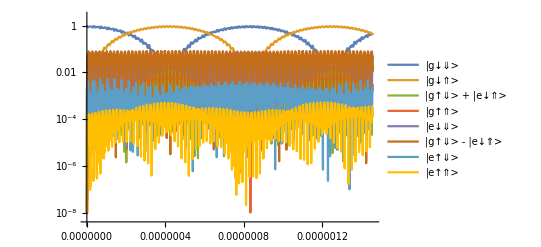

```mathematica
peakP[1.0277830043240364*^8, 9.947389096230388*^7]
Eac
Bac
LogPlot[Evaluate@Table[Max[Abs[state[[i]]]^2, 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All, PlotLegends->basisGERotated]
```

0.00155609 Cos[3.46363×10^10 t]

-6.51356+12 Cos[3.48385×10^10 t]

4.27×10^-7

0.959112

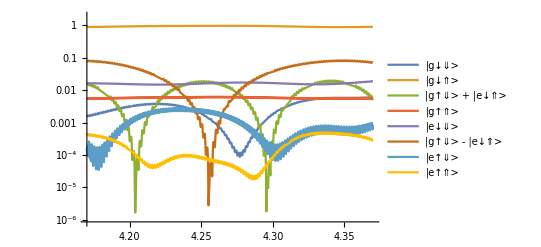

```mathematica
Eac = 12*Cos[(ω2 + δ2)*t] + (7.74736821604787*^7 - 1.8243496972178563*^8)/(2*8.057132424585237*^6 );
 Bac = a*12*((8.057132424585237*^6)/(6.213371789014474*^10))Cos[(ω1 + δ1)*t];
Bac /. δ1-> 1.0277830043240364*^8
Eac /. δ2 -> 9.947389096230388*^7

bestT = 0;
bestP = 0;
Do[
p = (Abs[state /. t->tt]^2)[[2]];
If[p > bestP, (
bestP = p;
bestT = tt // N;
)]
,{tt, 0, .5*10^-6, 10^-9}]

bestT
bestP

LogPlot[Evaluate@Table[Max[Abs[state[[i]]]^2, 10^-8], {i, Length[state]}],{t,bestT - 10^-8, bestT + 10^-8}, PlotRange->All, PlotLegends->basisGERotated]
```